## Paths and Includes

```mathematica
SetOptions[$FrontEnd,"CommonDefaultFormatTypes"->{"Output"->StandardForm}]
```

```mathematica
basepath=$HomeDirectory<>"/sivers_TMD_PhD_project/mathematica_hari"
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/mathematica_hari

```mathematica
SetDirectory[basepath<>"/output"];
```

```mathematica
includepath=basepath<>"/include";
AppendTo[$Path, includepath];
```

```mathematica
Needs["LatticeAnalysis`"];
```

```mathematica
<<"LatticeAnalysis`"
```

```mathematica
(* do not keep track of intermediate results *)
$HistoryLength=0;
```

## Configuration

We must provide information about the lattice spacing of the ensemble ourselves; it is not in the data base files (obviously)

```mathematica
lata=0.11403
```

0.11403

## Open Database

open the BIDATEX data base with the correlator data

```mathematica
dbNo = 1;
platdb=BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_"<>ToString[dbNo]<>"/UminusD_Plateaus_jn.bidatex"]
(*platdbPm2=BIDATEXReader[exportdatapath2[thisquarkchannel]<>"Plateaus"<>resamplingext<>".bidatex"]
platdbPm3=BIDATEXReader[exportdatapath3[thisquarkchannel]<>"Plateaus"<>resamplingext<>".bidatex"]
platdbPm4=BIDATEXReader[exportdatapath4[thisquarkchannel]<>"Plateaus"<>resamplingext<>".bidatex"]*)
NEdb=BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_"<>ToString[dbNo]<>"/NucleonEnergy_jn.bidatex"]
(*NEdb2=BIDATEXReader[basedatapath2<>"NucleonEnergy"<>resamplingext<>".bidatex"]
NEdb3=BIDATEXReader[basedatapath3<>"NucleonEnergy"<>resamplingext<>".bidatex"]
NEdb4=BIDATEXReader[basedatapath4<>"NucleonEnergy"<>resamplingext<>".bidatex"]*)
```

< -MemDB- {aBDBIndex,correlatorType,gammaValue,linkPath,momTransfer,numberFilter,section,seqPropNum,sideExtent,sideLink,sideNum,sinkMom,sourceType,tSep,tSink,tSource,analysisStep,data}>

< -MemDB- {gammaValue,operation,section,sinkMom,sourceType,comment,tSource,sideLinks,linkPath,sideNum,sideExtent,correlatorType,seqPropNum,tSink,momTransfer,latsizeOrig,latsizeChopped,baryonObservableNr,aBDBIndex,data,numberFilter,energy,chisqrPDOF}>

```mathematica
vlink = Union[MemDBGet[platdb,MemDBSelect[platdb,{numberFilter->Re}],sideLink]];
vlinksv1 = Select[vlink,Count[#,3]==0&];
vlinksv1
MemDBGet[platdb,MemDBSelect[platdb,{sideLink->{}}],linkPath]//Union
blink = Union[MemDBGet[platdb,MemDBSelect[platdb,{linkPath->{}}],sideLink]]
```

{{},{1},{1,1},{1,1,1},{1,1,1,1},{1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

{{},{-2},{2},{-2,-2},{-2,-1},{-2,1},{-1,-2},{-1,2},{1,-2},{1,2},{2,-1},{2,1},{2,2},{-2,-2,-2},{-2,-1,-2},{-2,1,-2},{-1,-2,-1},{-1,2,-1},{1,-2,1},{1,2,1},{2,-1,2},{2,1,2},{2,2,2},{-2,-2,-2,-2},{-2,-1,-2,-1},{-2,1,-2,1},{-1,-2,-1,-2},{-1,2,-1,2},{1,-2,1,-2},{1,2,1,2},{2,-1,2,-1},{2,1,2,1},{2,2,2,2},{-2,-2,-2,-2,-2},{-1,-1,-2,-1,-1},{-1,-1,2,-1,-1},{1,1,-2,1,1},{1,1,2,1,1},{2,2,2,2,2},{-2,-2,-2,-2,-2,-2},{-2,-1,-2,-2,-1,-2},{-2,-1,-2,-1,-2,-1},{-2,1,-2,-2,1,-2},{-2,1,-2,1,-2,1},{-1,-2,-1,-2,-1,-2},{-1,-2,-1,-1,-2,-1},{-1,2,-1,-1,2,-1},{-1,2,-1,2,-1,2},{1,-2,1,-2,1,-2},{1,-2,1,1,-2,1},{1,2,1,1,2,1},{1,2,1,2,1,2},{2,-1,2,-1,2,-1},{2,-1,2,2,-1,2},{2,1,2,1,2,1},{2,1,2,2,1,2},{2,2,2,2,2,2},{-2,-2,-2,-2,-2,-2,-2},{2,2,2,2,2,2,2},{-2,-1,-2,-1,-2,-1,-2,-1},{-2,1,-2,1,-2,1,-2,1},{-1,-2,-1,-2,-1,-2,-1,-2},{-1,2,-1,2,-1,2,-1,2},{1,-2,1,-2,1,-2,1,-2},{1,2,1,2,1,2,1,2},{2,-1,2,-1,2,-1,2,-1},{2,1,2,1,2,1,2,1},{-2,-1,-2,-2,-1,-2,-2,-1,-2},{-2,1,-2,-2,1,-2,-2,1,-2},{-1,-2,-1,-1,-2,-1,-1,-2,-1},{-1,2,-1,-1,2,-1,-1,2,-1},{1,-2,1,1,-2,1,1,-2,1},{1,2,1,1,2,1,1,2,1},{2,-1,2,2,-1,2,2,-1,2},{2,1,2,2,1,2,2,1,2},{-2,-1,-2,-1,-2,-1,-2,-1,-2,-1},{-2,1,-2,1,-2,1,-2,1,-2,1},{-1,-2,-1,-2,-1,-2,-1,-2,-1,-2},{-1,-1,-2,-1,-1,-1,-1,-2,-1,-1},{-1,-1,2,-1,-1,-1,-1,2,-1,-1},{-1,2,-1,2,-1,2,-1,2,-1,2},{1,-2,1,-2,1,-2,1,-2,1,-2},{1,1,-2,1,1,1,1,-2,1,1},{1,1,2,1,1,1,1,2,1,1},{1,2,1,2,1,2,1,2,1,2},{2,-1,2,-1,2,-1,2,-1,2,-1},{2,1,2,1,2,1,2,1,2,1}}

{{}}

```mathematica
AllLinkPathList = MemDBGet[platdb,MemDBSelect[platdb,{}],linkPath];
Print[ "Total No. linkPath = ",Length[AllLinkPathList]]
Print[ "Total No. Distinct linkPath = ",CountDistinct[AllLinkPathList]]
DistinctLinkPaths= DeleteDuplicates[AllLinkPathList];
Print["linkPath -> {} is skipped"];
bveclinkPathsideNumLIST={};
Do[
AppendTo[bveclinkPathsideNumLIST,{PathToShift[DistinctLinkPaths[[i+1]],3],DistinctLinkPaths[[i+1]]}],{i,CountDistinct[AllLinkPathList]-1}] (* i+1 is to skipp linkPath {} *)


bveclinkPathsideNumLISTforbpositive1=Select[bveclinkPathsideNumLIST,(#[[1,1]]==0&&#[[1,2]]>0)&];
bveclinkPathsideNumLISTforbpositive2=Select[bveclinkPathsideNumLIST,(#[[1,1]]>0&&#[[1,2]]>0)&];
bveclinkPathsideNumLISTforbpositive3=Select[bveclinkPathsideNumLIST,(#[[1,1]]>0&&#[[1,2]]<0)&];

bveclinkPathsideNumLISTforbnegative1=Select[bveclinkPathsideNumLIST,(#[[1,1]]==0&&#[[1,2]]<0)&];
bveclinkPathsideNumLISTforbnegative2=Select[bveclinkPathsideNumLIST,(#[[1,1]]<0&&#[[1,2]]<0)&];
bveclinkPathsideNumLISTforbnegative3=Select[bveclinkPathsideNumLIST,(#[[1,1]]<0&&#[[1,2]]>0)&];

bveclinkPathsideNumLISTforbpositive=Join[bveclinkPathsideNumLISTforbpositive1,bveclinkPathsideNumLISTforbpositive2,bveclinkPathsideNumLISTforbpositive3,bveclinkPathsideNumLISTforbnegative1,bveclinkPathsideNumLISTforbnegative2,bveclinkPathsideNumLISTforbnegative3];
bveclinkPathsideNumLISTforbnegative=Join[bveclinkPathsideNumLISTforbnegative1,bveclinkPathsideNumLISTforbnegative2,bveclinkPathsideNumLISTforbnegative3,bveclinkPathsideNumLISTforbpositive1,bveclinkPathsideNumLISTforbpositive2,bveclinkPathsideNumLISTforbpositive3];
bveclinkPathsideNumLISTforbpositive//MatrixForm
bveclinkPathsideNumLISTforbnegative//MatrixForm
Length[bveclinkPathsideNumLISTforbpositive]
Length[bveclinkPathsideNumLISTforbnegative]
noError=True;

Do[If[(bveclinkPathsideNumLISTforbpositive[[i,1]][[1]]+bveclinkPathsideNumLISTforbnegative[[i,1]][[1]])=!=0||(bveclinkPathsideNumLISTforbpositive[[i,1]][[2]]+bveclinkPathsideNumLISTforbnegative[[i,1]][[2]])=!=0,Print["Mismatch in finding at bveclinkPathsideNumLISTforbLpositive[",i,"]"];
noError=False;],{i,Length[bveclinkPathsideNumLISTforbpositive]}];

If[noError,Print["✓ Checked: linkPaths corresponding to +b & -b} are found"]]
```

Total No. linkPath = 57800

Total No. Distinct linkPath = 87

linkPath -> {} is skipped

({0,1,0} | {2}
{0,2,0} | {2,2}
{0,3,0} | {2,2,2}
{0,4,0} | {2,2,2,2}
{0,5,0} | {2,2,2,2,2}
{0,6,0} | {2,2,2,2,2,2}
{0,7,0} | {2,2,2,2,2,2,2}
{1,1,0} | {2,1}
{2,2,0} | {2,1,2,1}
{3,3,0} | {2,1,2,1,2,1}
{4,4,0} | {2,1,2,1,2,1,2,1}
{5,5,0} | {2,1,2,1,2,1,2,1,2,1}
{1,1,0} | {1,2}
{2,2,0} | {1,2,1,2}
{3,3,0} | {1,2,1,2,1,2}
{4,4,0} | {1,2,1,2,1,2,1,2}
{5,5,0} | {1,2,1,2,1,2,1,2,1,2}
{1,2,0} | {2,1,2}
{2,4,0} | {2,1,2,2,1,2}
{3,6,0} | {2,1,2,2,1,2,2,1,2}
{2,1,0} | {1,2,1}
{4,2,0} | {1,2,1,1,2,1}
{6,3,0} | {1,2,1,1,2,1,1,2,1}
{4,1,0} | {1,1,2,1,1}
{8,2,0} | {1,1,2,1,1,1,1,2,1,1}
{1,-1,0} | {-2,1}
{2,-2,0} | {-2,1,-2,1}
{3,-3,0} | {-2,1,-2,1,-2,1}
{4,-4,0} | {-2,1,-2,1,-2,1,-2,1}
{5,-5,0} | {-2,1,-2,1,-2,1,-2,1,-2,1}
{1,-1,0} | {1,-2}
{2,-2,0} | {1,-2,1,-2}
{3,-3,0} | {1,-2,1,-2,1,-2}
{4,-4,0} | {1,-2,1,-2,1,-2,1,-2}
{5,-5,0} | {1,-2,1,-2,1,-2,1,-2,1,-2}
{1,-2,0} | {-2,1,-2}
{2,-4,0} | {-2,1,-2,-2,1,-2}
{3,-6,0} | {-2,1,-2,-2,1,-2,-2,1,-2}
{2,-1,0} | {1,-2,1}
{4,-2,0} | {1,-2,1,1,-2,1}
{6,-3,0} | {1,-2,1,1,-2,1,1,-2,1}
{4,-1,0} | {1,1,-2,1,1}
{8,-2,0} | {1,1,-2,1,1,1,1,-2,1,1}
{0,-1,0} | {-2}
{0,-2,0} | {-2,-2}
{0,-3,0} | {-2,-2,-2}
{0,-4,0} | {-2,-2,-2,-2}
{0,-5,0} | {-2,-2,-2,-2,-2}
{0,-6,0} | {-2,-2,-2,-2,-2,-2}
{0,-7,0} | {-2,-2,-2,-2,-2,-2,-2}
{-1,-1,0} | {-2,-1}
{-2,-2,0} | {-2,-1,-2,-1}
{-3,-3,0} | {-2,-1,-2,-1,-2,-1}
{-4,-4,0} | {-2,-1,-2,-1,-2,-1,-2,-1}
{-5,-5,0} | {-2,-1,-2,-1,-2,-1,-2,-1,-2,-1}
{-1,-1,0} | {-1,-2}
{-2,-2,0} | {-1,-2,-1,-2}
{-3,-3,0} | {-1,-2,-1,-2,-1,-2}
{-4,-4,0} | {-1,-2,-1,-2,-1,-2,-1,-2}
{-5,-5,0} | {-1,-2,-1,-2,-1,-2,-1,-2,-1,-2}
{-1,-2,0} | {-2,-1,-2}
{-2,-4,0} | {-2,-1,-2,-2,-1,-2}
{-3,-6,0} | {-2,-1,-2,-2,-1,-2,-2,-1,-2}
{-2,-1,0} | {-1,-2,-1}
{-4,-2,0} | {-1,-2,-1,-1,-2,-1}
{-6,-3,0} | {-1,-2,-1,-1,-2,-1,-1,-2,-1}
{-4,-1,0} | {-1,-1,-2,-1,-1}
{-8,-2,0} | {-1,-1,-2,-1,-1,-1,-1,-2,-1,-1}
{-1,1,0} | {2,-1}
{-2,2,0} | {2,-1,2,-1}
{-3,3,0} | {2,-1,2,-1,2,-1}
{-4,4,0} | {2,-1,2,-1,2,-1,2,-1}
{-5,5,0} | {2,-1,2,-1,2,-1,2,-1,2,-1}
{-1,1,0} | {-1,2}
{-2,2,0} | {-1,2,-1,2}
{-3,3,0} | {-1,2,-1,2,-1,2}
{-4,4,0} | {-1,2,-1,2,-1,2,-1,2}
{-5,5,0} | {-1,2,-1,2,-1,2,-1,2,-1,2}
{-1,2,0} | {2,-1,2}
{-2,4,0} | {2,-1,2,2,-1,2}
{-3,6,0} | {2,-1,2,2,-1,2,2,-1,2}
{-2,1,0} | {-1,2,-1}
{-4,2,0} | {-1,2,-1,-1,2,-1}
{-6,3,0} | {-1,2,-1,-1,2,-1,-1,2,-1}
{-4,1,0} | {-1,-1,2,-1,-1}
{-8,2,0} | {-1,-1,2,-1,-1,-1,-1,2,-1,-1})

({0,-1,0} | {-2}
{0,-2,0} | {-2,-2}
{0,-3,0} | {-2,-2,-2}
{0,-4,0} | {-2,-2,-2,-2}
{0,-5,0} | {-2,-2,-2,-2,-2}
{0,-6,0} | {-2,-2,-2,-2,-2,-2}
{0,-7,0} | {-2,-2,-2,-2,-2,-2,-2}
{-1,-1,0} | {-2,-1}
{-2,-2,0} | {-2,-1,-2,-1}
{-3,-3,0} | {-2,-1,-2,-1,-2,-1}
{-4,-4,0} | {-2,-1,-2,-1,-2,-1,-2,-1}
{-5,-5,0} | {-2,-1,-2,-1,-2,-1,-2,-1,-2,-1}
{-1,-1,0} | {-1,-2}
{-2,-2,0} | {-1,-2,-1,-2}
{-3,-3,0} | {-1,-2,-1,-2,-1,-2}
{-4,-4,0} | {-1,-2,-1,-2,-1,-2,-1,-2}
{-5,-5,0} | {-1,-2,-1,-2,-1,-2,-1,-2,-1,-2}
{-1,-2,0} | {-2,-1,-2}
{-2,-4,0} | {-2,-1,-2,-2,-1,-2}
{-3,-6,0} | {-2,-1,-2,-2,-1,-2,-2,-1,-2}
{-2,-1,0} | {-1,-2,-1}
{-4,-2,0} | {-1,-2,-1,-1,-2,-1}
{-6,-3,0} | {-1,-2,-1,-1,-2,-1,-1,-2,-1}
{-4,-1,0} | {-1,-1,-2,-1,-1}
{-8,-2,0} | {-1,-1,-2,-1,-1,-1,-1,-2,-1,-1}
{-1,1,0} | {2,-1}
{-2,2,0} | {2,-1,2,-1}
{-3,3,0} | {2,-1,2,-1,2,-1}
{-4,4,0} | {2,-1,2,-1,2,-1,2,-1}
{-5,5,0} | {2,-1,2,-1,2,-1,2,-1,2,-1}
{-1,1,0} | {-1,2}
{-2,2,0} | {-1,2,-1,2}
{-3,3,0} | {-1,2,-1,2,-1,2}
{-4,4,0} | {-1,2,-1,2,-1,2,-1,2}
{-5,5,0} | {-1,2,-1,2,-1,2,-1,2,-1,2}
{-1,2,0} | {2,-1,2}
{-2,4,0} | {2,-1,2,2,-1,2}
{-3,6,0} | {2,-1,2,2,-1,2,2,-1,2}
{-2,1,0} | {-1,2,-1}
{-4,2,0} | {-1,2,-1,-1,2,-1}
{-6,3,0} | {-1,2,-1,-1,2,-1,-1,2,-1}
{-4,1,0} | {-1,-1,2,-1,-1}
{-8,2,0} | {-1,-1,2,-1,-1,-1,-1,2,-1,-1}
{0,1,0} | {2}
{0,2,0} | {2,2}
{0,3,0} | {2,2,2}
{0,4,0} | {2,2,2,2}
{0,5,0} | {2,2,2,2,2}
{0,6,0} | {2,2,2,2,2,2}
{0,7,0} | {2,2,2,2,2,2,2}
{1,1,0} | {2,1}
{2,2,0} | {2,1,2,1}
{3,3,0} | {2,1,2,1,2,1}
{4,4,0} | {2,1,2,1,2,1,2,1}
{5,5,0} | {2,1,2,1,2,1,2,1,2,1}
{1,1,0} | {1,2}
{2,2,0} | {1,2,1,2}
{3,3,0} | {1,2,1,2,1,2}
{4,4,0} | {1,2,1,2,1,2,1,2}
{5,5,0} | {1,2,1,2,1,2,1,2,1,2}
{1,2,0} | {2,1,2}
{2,4,0} | {2,1,2,2,1,2}
{3,6,0} | {2,1,2,2,1,2,2,1,2}
{2,1,0} | {1,2,1}
{4,2,0} | {1,2,1,1,2,1}
{6,3,0} | {1,2,1,1,2,1,1,2,1}
{4,1,0} | {1,1,2,1,1}
{8,2,0} | {1,1,2,1,1,1,1,2,1,1}
{1,-1,0} | {-2,1}
{2,-2,0} | {-2,1,-2,1}
{3,-3,0} | {-2,1,-2,1,-2,1}
{4,-4,0} | {-2,1,-2,1,-2,1,-2,1}
{5,-5,0} | {-2,1,-2,1,-2,1,-2,1,-2,1}
{1,-1,0} | {1,-2}
{2,-2,0} | {1,-2,1,-2}
{3,-3,0} | {1,-2,1,-2,1,-2}
{4,-4,0} | {1,-2,1,-2,1,-2,1,-2}
{5,-5,0} | {1,-2,1,-2,1,-2,1,-2,1,-2}
{1,-2,0} | {-2,1,-2}
{2,-4,0} | {-2,1,-2,-2,1,-2}
{3,-6,0} | {-2,1,-2,-2,1,-2,-2,1,-2}
{2,-1,0} | {1,-2,1}
{4,-2,0} | {1,-2,1,1,-2,1}
{6,-3,0} | {1,-2,1,1,-2,1,1,-2,1}
{4,-1,0} | {1,1,-2,1,1}
{8,-2,0} | {1,1,-2,1,1,1,1,-2,1,1})

86

86

✓ Checked: linkPaths corresponding to +b & -b} are found

```mathematica
ztahat=Sqrt[(P1*P1)/(M*M*(((M*M)/(P1*P1))+(2*II)))];
Rztahatsquare = II-Sqrt[II+(II/(ztahat*ztahat))] ;
v1byv3jakk=(M*ztahat)/(Sqrt[(P1*P1)-(M*M*ztahat*ztahat)]);
v1BYv3=Abs[MakeErrBars[{{1,v1byv3jakk}}][[1]][[1]][[2]]];
v1[v3_]:=v3*v1BYv3;

vinterpolation[gammaValueI_,numberFilterI_, linkPathI_, eta_]:=
(
vlinks = Union[MemDBGet[platdb,MemDBSelect[platdb,{numberFilter->Re}],sideLink]];
vlinksv3 = Select[vlinks,Count[#,3]==eta&];
vvectoranddata={};
Do[
v1data=PathToShift[vlinksv3[[i]],3];
correlatordata = MemDBGet[platdb,MemDBSelect[platdb,{gammaValue->gammaValueI,numberFilter->numberFilterI,linkPath->linkPathI,sideLink->vlinksv3[[i]]}],data];
AppendTo[vvectoranddata,{v1data,correlatordata[[1]]}]
,{i,Length[vlinksv3]}];
groupSamev=GroupBy[vvectoranddata,First->Last];
averagedTableEvengPlusImForv=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSamev];
(*Print[averagedTableEvengPlusImForv//OutputForm];*)
dataforInterpolation ={};
v1dataforInterpolation ={};
Do[
AppendTo[v1dataforInterpolation,v1[averagedTableEvengPlusImForv[[i]][[1]][[3]]]-averagedTableEvengPlusImForv[[i]][[1]][[1]]];
AppendTo[dataforInterpolation,averagedTableEvengPlusImForv[[i]][[2]]];
,{i, Length[averagedTableEvengPlusImForv]}];
(*Print[Transpose[{v1dataforInterpolation,dataforInterpolation}]//OutputForm];*)
fninterpol = Interpolation[Transpose[{v1dataforInterpolation,dataforInterpolation}],InterpolationOrder->2];
Return[fninterpol[0]];
);
A= vinterpolation[gammaValueI = 8,numberFilterI = Im, linkPathI = {2,1}, eta = 8]
B =vinterpolation[gammaValueI = 8,numberFilterI = Im, linkPathI = {-2,-1}, eta = 8]
A+B
A-B
```

⟨0.0319(28)⟩_(RowBox[{)

⟨-0.0306(30)⟩_(RowBox[{)

⟨0.0013(52)⟩_(RowBox[{)

⟨0.0625(26)⟩_(RowBox[{)

```mathematica
NewDBforAbLbT=NewMemDB[];
NewDBforAbPb2 = NewMemDB[];
Print["dbNo = ", dbNo];
P0= MemDBGet[NEdb,MemDBSelect[NEdb,{}],energy][[1]]; (* P0 = EN *)
II=(P0/P0);
P1 = dbNo*II*((2*Pi)/(32)); (* P1 = |P1| *)
Msquare =(P0*P0)-(P1*P1);
M =Sqrt[Msquare];

ztahat=Sqrt[(P1*P1)/(M*M*(((M*M)/(P1*P1))+(2*II)))];
Rztahatsquare = II-Sqrt[II+(II/(ztahat*ztahat))] ;
v1byv3jakk=(M*ztahat)/(Sqrt[(P1*P1)-(M*M*ztahat*ztahat)]);
v1BYv3=Abs[MakeErrBars[{{1,v1byv3jakk}}][[1]][[1]][[2]]];
v1[v3_]:=v3*v1BYv3;

vinterpolation[gammaValueI_,numberFilterI_, linkPathI_, eta_]:=
(
vlinks = Union[MemDBGet[platdb,MemDBSelect[platdb,{numberFilter->Re}],sideLink]];
vlinksv3 = Select[vlinks,Count[#,3]==eta&];
vvectoranddata={};
Do[
v1data=PathToShift[vlinksv3[[i]],3];
correlatordata = MemDBGet[platdb,MemDBSelect[platdb,{gammaValue->gammaValueI,numberFilter->numberFilterI,linkPath->linkPathI,sideLink->vlinksv3[[i]]}],data];
AppendTo[vvectoranddata,{v1data,correlatordata[[1]]}]
,{i,Length[vlinksv3]}];
groupSamev=GroupBy[vvectoranddata,First->Last];
averagedTableEvengPlusImForv=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSamev];
(*Print[averagedTableEvengPlusImForv//OutputForm];*)
dataforInterpolation ={};
v1dataforInterpolation ={};
Do[
AppendTo[v1dataforInterpolation,v1[averagedTableEvengPlusImForv[[i]][[1]][[3]]]-averagedTableEvengPlusImForv[[i]][[1]][[1]]];
AppendTo[dataforInterpolation,averagedTableEvengPlusImForv[[i]][[2]]];
,{i, Length[averagedTableEvengPlusImForv]}];
(*Print[Transpose[{v1dataforInterpolation,dataforInterpolation}]//OutputForm];*)
fninterpol = Interpolation[Transpose[{v1dataforInterpolation,dataforInterpolation}],InterpolationOrder->2];
Return[fninterpol[0]];
);

Do[
bvectorA12Bevenb = {};
bvectorA12Boddb = {};
bvectorA2Bevenb  = {};
bvectorA2Boddb = {};

b0g8Re =MemDBGet[platdb,MemDBSelect[platdb,{linkPath->{}, gammaValue->8, numberFilter->Re}],data][[1]];
b0g4Im = MemDBGet[platdb,MemDBSelect[platdb,{linkPath->{}, gammaValue->4, numberFilter->Im}],data][[1]];
b0A2=b0g8Re/2;
b0B1=((P0*P1*v1byv3jakk)/(2*M*M))*b0g4Im;
b0A2B =b0A2+( Rztahatsquare*b0B1);
AppendTo[bvectorA2Bevenb,{{0,0,0},b0A2B}];
AppendTo[bvectorA2Boddb,{{0,0,0},0*b0A2B}];

Do[
bPg8Im = vinterpolation[gammaValueI = 8,numberFilterI = Im, linkPathI = bveclinkPathsideNumLISTforbpositive[[i,2]], eta = etavalue];
bPg8Re = vinterpolation[gammaValueI = 8,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbpositive[[i,2]], eta = etavalue];
bPg1Re = vinterpolation[gammaValueI = 1,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbpositive[[i,2]], eta = etavalue];
bPg1Im = vinterpolation[gammaValueI = 1,numberFilterI = Im, linkPathI = bveclinkPathsideNumLISTforbpositive[[i,2]], eta = etavalue];
bPg2Re = vinterpolation[gammaValueI = 2,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbpositive[[i,2]], eta = etavalue];
bPg2Im = vinterpolation[gammaValueI = 2,numberFilterI = Im, linkPathI = bveclinkPathsideNumLISTforbpositive[[i,2]], eta = etavalue];
bPg4Re = vinterpolation[gammaValueI = 4,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbpositive[[i,2]], eta = etavalue];
bPg4Im = vinterpolation[gammaValueI = 4,numberFilterI = Im, linkPathI = bveclinkPathsideNumLISTforbpositive[[i,2]], eta = etavalue];

bNg8Im=vinterpolation[gammaValueI = 8,numberFilterI = Im, linkPathI = bveclinkPathsideNumLISTforbnegative[[i,2]], eta = etavalue];
bNg8Re=vinterpolation[gammaValueI = 8,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbnegative[[i,2]], eta = etavalue];
bNg1Re=vinterpolation[gammaValueI = 1,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbnegative[[i,2]], eta = etavalue];
bNg1Im=vinterpolation[gammaValueI = 1,numberFilterI = Im, linkPathI = bveclinkPathsideNumLISTforbnegative[[i,2]], eta = etavalue];
bNg2Re=vinterpolation[gammaValueI = 2,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbnegative[[i,2]], eta = etavalue];
bNg2Im=vinterpolation[gammaValueI = 2,numberFilterI = Im, linkPathI = bveclinkPathsideNumLISTforbnegative[[i,2]], eta = etavalue];
bNg4Re=vinterpolation[gammaValueI = 4,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbnegative[[i,2]], eta = etavalue];
bNg4Im=vinterpolation[gammaValueI = 4,numberFilterI = Im, linkPathI = bveclinkPathsideNumLISTforbnegative[[i,2]], eta = etavalue];

Img8even = (bPg8Im+bNg8Im)/2;
Img8odd = (bPg8Im-bNg8Im)/2;
Reg8even = (bPg8Re+bNg8Re)/2;
Reg8odd = (bPg8Re-bNg8Re)/2;

Img1even = (bPg1Im+bNg1Im)/2;
Img1odd = (bPg1Im-bNg1Im)/2;
Reg1even = (bPg1Re+bNg1Re)/2;
Reg1odd = (bPg1Re-bNg1Re)/2;

Img2even = (bPg2Im+bNg2Im)/2;
Img2odd = (bPg2Im-bNg2Im)/2;
Reg2even = (bPg2Re+bNg2Re)/2;
Reg2odd = (bPg2Re-bNg2Re)/2;

Img4even = (bPg4Im+bNg4Im)/2;
Img4odd = (bPg4Im-bNg4Im)/2;
Reg4even = (bPg4Re+bNg4Re)/2;
Reg4odd = (bPg4Re-bNg4Re)/2;

b2valuebP= bveclinkPathsideNumLISTforbpositive[[i,1]][[2]];
b1valuebP= bveclinkPathsideNumLISTforbpositive[[i,1]][[1]];

A2Re=(1/2)*Reg8even;
B1Re=((P0*P1*v1byv3jakk)/(2*M*M))*Img4even;
A12Re=(-b2valuebP/(2*M*(b2valuebP*b2valuebP+b1valuebP*b1valuebP)))*(Reg1odd+(b1valuebP*Reg2odd/b2valuebP)+((b2valuebP*b2valuebP+b1valuebP*b1valuebP)*Reg4odd/(b2valuebP*b2valuebP*v1byv3jakk)));
B8Re=(-P1/(2*M*M*M*b2valuebP))*((P0*Img8odd)+(P1*Reg4odd/v1byv3jakk)+(2*M*P1*b2valuebP*A12Re));

A2Im=(1/2)*Img8even;
B1Im=((P0*P1*v1byv3jakk)/(2*M*M))*Reg4even;
A12Im=(-b2valuebP/(2*M*(b2valuebP*b2valuebP+b1valuebP*b1valuebP)))*(Img1odd+(b1valuebP*Img2odd/b2valuebP)+((b2valuebP*b2valuebP+b1valuebP*b1valuebP)*Img4odd/(b2valuebP*b2valuebP*v1byv3jakk)));
B8Im=(P1/(2*M*M*M*b2valuebP))*((P0*Reg8odd)-(P1*Img4odd/v1byv3jakk)-(2*M*P1*b2valuebP*A12Im));

ReA2B =A2Re+( Rztahatsquare*B1Re);
ImA2B =A2Im+( Rztahatsquare*B1Im);

ReA12B=A12Re-(Rztahatsquare*B8Re);
ImA12B=A12Im-(Rztahatsquare*B8Im);



AppendTo[bvectorA12Bevenb,{bveclinkPathsideNumLISTforbpositive[[i,1]],ReA12B}];

AppendTo[bvectorA12Boddb,{bveclinkPathsideNumLISTforbpositive[[i,1]],ImA12B}];

AppendTo[bvectorA2Bevenb,{bveclinkPathsideNumLISTforbpositive[[i,1]],ReA2B}];

AppendTo[bvectorA2Boddb,{bveclinkPathsideNumLISTforbpositive[[i,1]],ImA2B}];
,{i,Length[bveclinkPathsideNumLISTforbpositive]}];

groupSamebA12Bevenb=GroupBy[bvectorA12Bevenb,First->Last];
groupSamebA12Boddb=GroupBy[bvectorA12Boddb,First->Last];
(*save bL, bT, Amp*)
averagedSamebvectorA12Bevenb=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSamebA12Bevenb];
averagedSamebvectorA12Boddb=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSamebA12Boddb];
Do[
MemDBAppend[NewDBforAbLbT,{PL->-dbNo,etav->etavalue, bL->averagedSamebvectorA12Bevenb[[j]][[1]][[1]],bT->averagedSamebvectorA12Bevenb[[j]][[1]][[2]],A->"A12B",bNum->"even", zta->ztahat, MN->M, EN->P0,data->averagedSamebvectorA12Bevenb[[j]][[2]]}];
MemDBAppend[NewDBforAbLbT,{PL->-dbNo,etav->etavalue, bL->averagedSamebvectorA12Boddb[[j]][[1]][[1]],bT->averagedSamebvectorA12Boddb[[j]][[1]][[2]],A->"A12B",bNum->"odd", zta->ztahat, MN->M, EN->P0,data->averagedSamebvectorA12Boddb[[j]][[2]]}];
,{j,Length[averagedSamebvectorA12Boddb]}];

groupSamebA2Bevenb=GroupBy[bvectorA2Bevenb,First->Last];
groupSamebA2Boddb=GroupBy[bvectorA2Boddb,First->Last];
averagedSamebvectorA2Bevenb=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSamebA2Bevenb];
averagedSamebvectorA2Boddb=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSamebA2Boddb];
Do[
MemDBAppend[NewDBforAbLbT,{PL->-dbNo,etav->etavalue, bL->averagedSamebvectorA2Bevenb[[jj]][[1]][[1]],bT->averagedSamebvectorA2Bevenb[[jj]][[1]][[2]],A->"A2B",bNum->"even", zta->ztahat, MN->M, EN->P0,data->averagedSamebvectorA2Bevenb[[jj]][[2]]}];
MemDBAppend[NewDBforAbLbT,{PL->-dbNo,etav->etavalue, bL->averagedSamebvectorA2Boddb[[jj]][[1]][[1]],bT->averagedSamebvectorA2Boddb[[jj]][[1]][[2]],A->"A2B",bNum->"odd", zta->ztahat, MN->M, EN->P0,data->averagedSamebvectorA2Boddb[[jj]][[2]]}];
,{jj,Length[averagedSamebvectorA12Boddb]}];

(*save b.p, b^2, Amp*)
bPbsquareA12Bevenb={};
Do[
AppendTo[bPbsquareA12Bevenb,{{ -averagedSamebvectorA12Bevenb[[j]][[1]][[1]]*dbNo,((averagedSamebvectorA12Bevenb[[j]][[1]][[1]]*averagedSamebvectorA12Bevenb[[j]][[1]][[1]])+(averagedSamebvectorA12Bevenb[[j]][[1]][[2]]*averagedSamebvectorA12Bevenb[[j]][[1]][[2]]))},averagedSamebvectorA12Bevenb[[j]][[2]]}]
,{j,Length[averagedSamebvectorA12Bevenb]}];
groupSamebsquareA12Bevenb=GroupBy[bPbsquareA12Bevenb,First->Last];
PbaveragedSamebsquareA12Bevenb=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSamebsquareA12Bevenb];
Do[
MemDBAppend[NewDBforAbPb2,{PL->-dbNo,etav->etavalue, Pb32by2Pi->PbaveragedSamebsquareA12Bevenb[[j]][[1]][[1]],bsquare->PbaveragedSamebsquareA12Bevenb[[j]][[1]][[2]],A->"A12B",bNum->"even", zta->ztahat, MN->M, EN->P0,data->PbaveragedSamebsquareA12Bevenb[[j]][[2]]}];
,{j,Length[PbaveragedSamebsquareA12Bevenb]}];
bPbsquareA12Boddb={};
Do[
AppendTo[bPbsquareA12Boddb,{{ -averagedSamebvectorA12Boddb[[j]][[1]][[1]]*dbNo,((averagedSamebvectorA12Boddb[[j]][[1]][[1]]*averagedSamebvectorA12Boddb[[j]][[1]][[1]])+(averagedSamebvectorA12Boddb[[j]][[1]][[2]]*averagedSamebvectorA12Boddb[[j]][[1]][[2]]))},averagedSamebvectorA12Boddb[[j]][[2]]}]
,{j,Length[averagedSamebvectorA12Boddb]}];
groupSamebsquareA12Boddb=GroupBy[bPbsquareA12Boddb,First->Last];
PbaveragedSamebsquareA12Boddb=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSamebsquareA12Boddb];
Do[
MemDBAppend[NewDBforAbPb2,{PL->-dbNo,etav->etavalue, Pb32by2Pi->PbaveragedSamebsquareA12Boddb[[j]][[1]][[1]],bsquare->PbaveragedSamebsquareA12Boddb[[j]][[1]][[2]],A->"A12B",bNum->"odd", zta->ztahat, MN->M, EN->P0,data->PbaveragedSamebsquareA12Boddb[[j]][[2]]}];
,{j,Length[PbaveragedSamebsquareA12Boddb]}];

bPbsquareA2Bevenb={};
Do[
AppendTo[bPbsquareA2Bevenb,{{ -averagedSamebvectorA2Bevenb[[j]][[1]][[1]]*dbNo,((averagedSamebvectorA2Bevenb[[j]][[1]][[1]]*averagedSamebvectorA2Bevenb[[j]][[1]][[1]])+(averagedSamebvectorA2Bevenb[[j]][[1]][[2]]*averagedSamebvectorA2Bevenb[[j]][[1]][[2]]))},averagedSamebvectorA2Bevenb[[j]][[2]]}]
,{j,Length[averagedSamebvectorA2Bevenb]}];
groupSamebsquareA2Bevenb=GroupBy[bPbsquareA2Bevenb,First->Last];
PbaveragedSamebsquareA2Bevenb=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSamebsquareA2Bevenb];
Do[
MemDBAppend[NewDBforAbPb2,{PL->-dbNo,etav->etavalue, Pb32by2Pi->PbaveragedSamebsquareA2Bevenb[[j]][[1]][[1]],bsquare->PbaveragedSamebsquareA2Bevenb[[j]][[1]][[2]],A->"A2B",bNum->"even", zta->ztahat, MN->M, EN->P0,data->PbaveragedSamebsquareA2Bevenb[[j]][[2]]}];
,{j,Length[PbaveragedSamebsquareA2Bevenb]}];


bPbsquareA2Boddb={};
Do[
AppendTo[bPbsquareA2Boddb,{{ -averagedSamebvectorA2Boddb[[j]][[1]][[1]]*dbNo,((averagedSamebvectorA2Boddb[[j]][[1]][[1]]*averagedSamebvectorA2Boddb[[j]][[1]][[1]])+(averagedSamebvectorA2Boddb[[j]][[1]][[2]]*averagedSamebvectorA2Boddb[[j]][[1]][[2]]))},averagedSamebvectorA2Boddb[[j]][[2]]}]
,{j,Length[averagedSamebvectorA2Boddb]}];
groupSamebsquareA2Boddb=GroupBy[bPbsquareA2Boddb,First->Last];
PbaveragedSamebsquareA2Boddb=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSamebsquareA2Boddb];
Do[
MemDBAppend[NewDBforAbPb2,{PL->-dbNo,etav->etavalue, Pb32by2Pi->PbaveragedSamebsquareA2Boddb[[j]][[1]][[1]],bsquare->PbaveragedSamebsquareA2Boddb[[j]][[1]][[2]],A->"A2B",bNum->"odd", zta->ztahat, MN->M, EN->P0,data->PbaveragedSamebsquareA2Boddb[[j]][[2]]}];
,{j,Length[PbaveragedSamebsquareA2Boddb]}];
Print["eta = ", etavalue]
,{etavalue, 8, 8}]
```

dbNo = 1

$Aborted

```mathematica
BIDATEXWriter[NewDBforAbLbT,"/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_correct_try_A12B_A2B_bL_bT_bevenodd.bidatex"]
BIDATEXWriter[NewDBforAbPb2,"/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_correct_try_A12B_A2B_Pb32by2Pi_bsq_bevenodd.bidatex"]
```

```mathematica
DBnew = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_A12B_A2B_P_Pb32by2Pi_bsq.bidatex"]
Print[MemDBGet[DBnew,MemDBSelect[DBnew,{etav->8}],{PL, Pb32by2Pi}]//OutputForm]
```

$Aborted

ReplaceAll::reps: {MemDB`Private`KeyNameDispatch[DBnew]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {False} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

MemDB::invkey: Error: Unknown key names!

$Aborted

< -MemDB- {A,bL,bT,data,EN,etav,MN,PL,zta}>

{⟨0.0303(23)⟩_(2902J)}

```mathematica
(*MemDBGet[DBnew,MemDBSelect[DBnew,{}],EN]//Union*)
```

{⟨0.6530(27)⟩_(RowBox[{),⟨0.7389(42)⟩_(RowBox[{),⟨0.8546(74)⟩_(RowBox[{),⟨0.999(14)⟩_(RowBox[{)}

```mathematica
PlotA12B[etavalue_]:=(
TablePbbsquareA12B = GivebPbbsquareA12B[etavalue];
groupSamebsquare=GroupBy[TablePbbsquareA12B,First->Last];
PbaveragedbsquareA12B=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSamebsquare];
Print["\n etavalue = ", etavalue];
(*Print["✓ Same  with different linkPath are averaged\n"];*)
bsquarelist= Union[PbaveragedbsquareA12B[[All,1]][[All,2]]];
PbLlist= Union[PbaveragedbsquareA12B[[All,1]][[All,1]]];
PbA2BforDiffbsquare={};
Do[
PbA2B=Transpose[{Select[PbaveragedbsquareA12B, #[[1,2]]==bsquarelist[[i]]&][[All,1]][[All,1]],Select[PbaveragedbsquareA12B, #[[1,2]]==bsquarelist[[i]]&][[All,2]]}];
AppendTo[PbA2BforDiffbsquare,PbA2B];
 ,{i,Length[bsquarelist]}];
PltA12B= ErrorListPlot[Table[MakeErrBars[PbA2BforDiffbsquare[[b2]]],{b2, Length[bsquarelist]}],FrameLabel->{Style[,Large],Style[,Large]}, Frame->True ,PlotRange->All
, PlotLegends->Table[" = "<>ToString[bsquarelist[[b2]]],{b2,Length[bsquarelist]}]];
Return[Print[PltA12B]];
)

PbbsqA12Bvalueserrbars[etavalue_]:=(
PbbsqA12BvalueerrbarLIST={};
TablePbbsquareA12B = GivebPbbsquareA12B[etavalue];
groupSamebsquare=GroupBy[TablePbbsquareA12B,First->Last];
PbaveragedbsquareA12B=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSamebsquare];
PbbsqA12Bvalueerrbar = MakeErrBars[PbaveragedbsquareA12B];
Do[
AppendTo[PbbsqA12BvalueerrbarLIST, {etavalue, PbbsqA12Bvalueerrbar[[i]][[1]][[1]][[1]] ,PbbsqA12Bvalueerrbar[[i]][[1]][[1]][[2]],  PbbsqA12Bvalueerrbar[[i]][[1]][[2]],  PbbsqA12Bvalueerrbar[[i]][[2]][[1]][[2]]}];
,{i, Length[PbbsqA12Bvalueerrbar]}];
Return[PbbsqA12BvalueerrbarLIST]
)
```

etavalue = 8

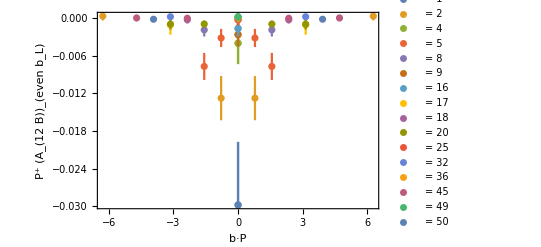

```mathematica
(*PlotA12B[8]*)
```

```mathematica
(*Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/eta_Pb_bsquare_A12B_err_AllMomentum.h5",Table["Pl-4/eta_"<>ToString[n]<>"_Pb_bsq_A12B_err"->PbbsqA12Bvalueserrbars[n],{n,1,10}],OverwriteTarget->"Append"]*)
```

```mathematica
BIDATEXWriter[M, "/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/test.bidatex"]
```

```mathematica
BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/test.bidatex"]
```

⟨0.617(22)⟩_(RowBox[{)

```mathematica
newDB=NewMemDB[];

Do[MemDBAppend[newDB,{p->-1,bL->bLval,bT->bTval,zta->ztaVal,data->M}],{bLval,{4,6,8}},(*Example values for bL*){bTval,{1,2,3}},(*Example values for bT*){ztaVal,{0.1,0.2,0.3}} (*Example values for zta*)];

BIDATEXWriter[newDB,"/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/tes2t.bidatex"]
```

```mathematica
newDB
```

< -MemDB- {bL,bT,data,p,zta}>

```mathematica
ttt = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/tes2t.bidatex"]
```

< -MemDB- {bL,bT,data,p,zta}>

```mathematica
MemDBGet[ttt,MemDBSelect[ttt,{}],{bL, zta,data}]
```

{{4,0.1,⟨0.617(22)⟩_(RowBox[{)},{4,0.2,⟨0.617(22)⟩_(RowBox[{)},{4,0.3,⟨0.617(22)⟩_(RowBox[{)},{4,0.1,⟨0.617(22)⟩_(RowBox[{)},{4,0.2,⟨0.617(22)⟩_(RowBox[{)},{4,0.3,⟨0.617(22)⟩_(RowBox[{)},{4,0.1,⟨0.617(22)⟩_(RowBox[{)},{4,0.2,⟨0.617(22)⟩_(RowBox[{)},{4,0.3,⟨0.617(22)⟩_(RowBox[{)},{6,0.1,⟨0.617(22)⟩_(RowBox[{)},{6,0.2,⟨0.617(22)⟩_(RowBox[{)},{6,0.3,⟨0.617(22)⟩_(RowBox[{)},{6,0.1,⟨0.617(22)⟩_(RowBox[{)},{6,0.2,⟨0.617(22)⟩_(RowBox[{)},{6,0.3,⟨0.617(22)⟩_(RowBox[{)},{6,0.1,⟨0.617(22)⟩_(RowBox[{)},{6,0.2,⟨0.617(22)⟩_(RowBox[{)},{6,0.3,⟨0.617(22)⟩_(RowBox[{)},{8,0.1,⟨0.617(22)⟩_(RowBox[{)},{8,0.2,⟨0.617(22)⟩_(RowBox[{)},{8,0.3,⟨0.617(22)⟩_(RowBox[{)},{8,0.1,⟨0.617(22)⟩_(RowBox[{)},{8,0.2,⟨0.617(22)⟩_(RowBox[{)},{8,0.3,⟨0.617(22)⟩_(RowBox[{)},{8,0.1,⟨0.617(22)⟩_(RowBox[{)},{8,0.2,⟨0.617(22)⟩_(RowBox[{)},{8,0.3,⟨0.617(22)⟩_(RowBox[{)}}

```mathematica
(*datafor2dGaussianFitbLbTerrors={};
Do[
dataPointErr=MakeErrBars[PlotbLforDiffbTList[[TagbT]]];
Do[
AppendTo[datafor2dGaussianFitbLbTerrors,{{dataPointErr[[All,1]][[TagbL]][[1]],bTlist[[TagbT]],dataPointErr[[All,1]][[TagbL]][[2]]},dataPointErr[[All,2,1]][[TagbL]]}];
,{TagbL,Length[dataPointErr]}];
,{TagbT,Length[bTlist]}];
points=datafor2dGaussianFitbLbTerrors[[All,1]];
errors=datafor2dGaussianFitbLbTerrors[[All,2]];
Print[datafor2dGaussianFitbLbTerrors]

fitbLbLbT=NonlinearModelFit[points,A*Exp[-((alpha*()^2)+(beta*()^2))],{A,alpha, beta},{,},Weights->1/(errors[[All,2]]^2),Method->"LevenbergMarquardt",MaxIterations->10000];
Print["Fitting into   = ",Normal[fitbLbLbT]];
Print["\n             Fit dependence in  space"];
PlotfitbLbT=Show[PlotbL,Table[Plot[fitbLbLbT[x,bT],{x,Min[bLlist],Max[bLlist]},PlotStyle->ColorData[97,"ColorList"][[bT]]],{bT,1,Length[bTlist]}]];
Print[PlotfitbLbT];
Print["\n                 Cast in ,  space"];
FnbdotPbsqre[bp_,b2_]:=(A/.fitbLbLbT["BestFitParameters"])*Exp[-((bp^2)*(alpha/.fitbLbLbT["BestFitParameters"]))-(((b2) - (bp^2))*(beta/.fitbLbLbT["BestFitParameters"]))];
bsquarelist={1,4,9,16,25};
PlotbLdata= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTList[[bT]]],{bT, Length[bTlist]}],FrameLabel->{Style[,Large],Style[,Large]}, Frame->True ,PlotLegends->Table[" = "<>ToString[bTlist[[bT]]],{bT,Length[bTlist]}]];
Cast=Show[PlotbLdata,Table[Plot[FnbdotPbsqre[x,bsq],{x,Min[bLlist],Max[bLlist]}, Frame->True],{bsq,bsquarelist}]];
Print[Cast];
Print[" = ",bsquarelist]
Print["\n                 Fourier transform "];
xFourierTransf[x_, b2_]:= FourierTransform[(A/.fitbLbLbT["BestFitParameters"])*Exp[-((bp^2)*(alpha/.fitbLbLbT["BestFitParameters"]))-(((b2) - (bp^2))*(beta/.fitbLbLbT["BestFitParameters"]))],bp,x];
xFourier=Show[Table[Plot[xFourierTransf[x,bsq],{x,0,1}, AxesLabel->{x,None}],{bsq,bsquarelist}]];
Print[xFourier];
Print["\n    Normalize to -integrated Sivers shift, multiply by "];
xFourier=Show[Table[Plot[-x*xFourierTransf[x,bsq],{x,0,1}, AxesLabel->{x,None}],{bsq,bsquarelist}]];
Print[xFourier];*)
```